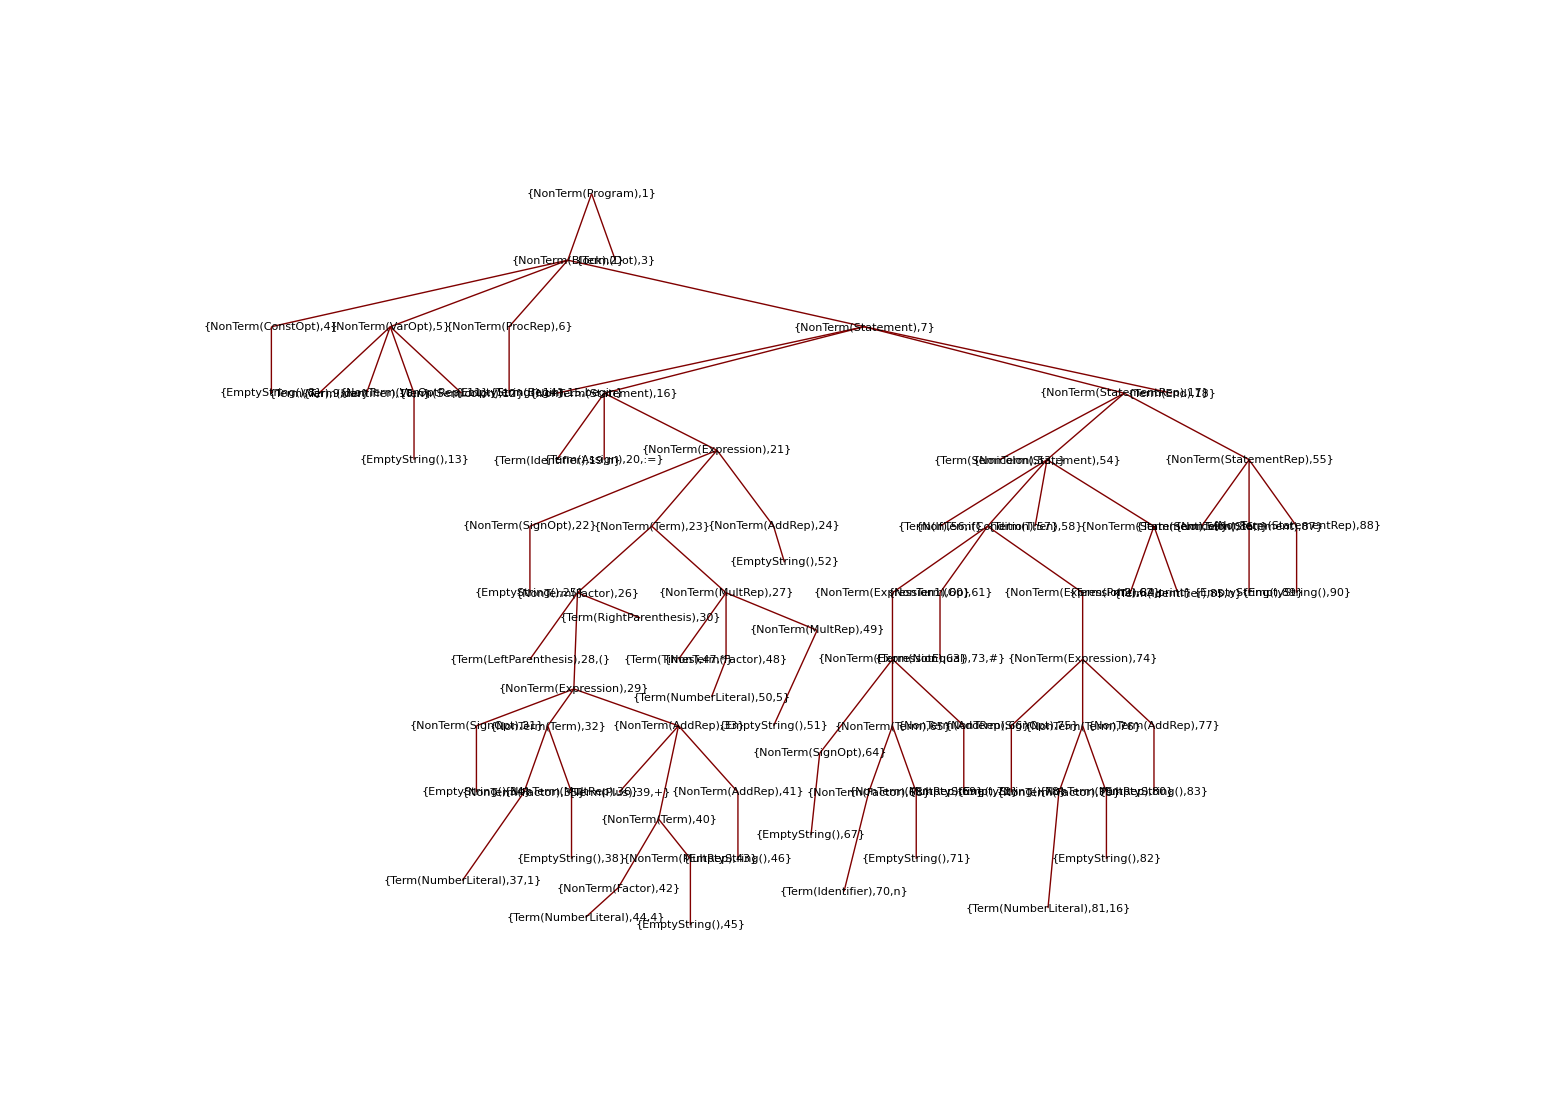

```mathematica
tinyProgram =
"var n;
begin
   n := (1+4)*5;
   if n # 16 then
      print n;
end.";
```

```mathematica
tokens = Tokenize[tinyProgram,symbolTokens,keywordDFA];
```

```mathematica
parseTree = Parse[tokens,grammar] ;
{NonTerm["Program"],1}["TACode"]/.SynthesizeTree[parseTree]
```

declare n
add 1 4 $0
multiply $0 5 $1
set n $1
not_equal n 16 $2
if_false $2 goto L$3
print n
label L$3
halt